# Branch Cuts

### ℝ and Inverse Trig

We had to choose basic domains for the trig functions in ℝ to define inverse trig functions.  The basic chunk for sine is usually [-π/2,π/2]

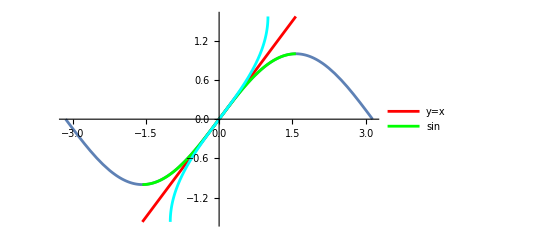

```mathematica
Show[
Plot[Sin[x],{x,-π,π}],
Plot[{x,Sin[x]},{x,-π/2,π/2},PlotStyle->{Red,Green} ,PlotLegends->{"y=x","sin"}],
Plot[ArcSin[x],{x,-1,1},PlotStyle->Cyan ],
PlotRange->All
]
```

### Log

In calculus log(-1) was not defined!  Since ⅇ^(z+ ⅈ 2π)=ⅇ^z. ⅇ^(2π ⅈ)=ⅇ^z we need to choose a basic chunk for the exponential function to define its inverse log(z).  A basic chunk here just means we should not wind all the way round the origin. The standard way to do this is just to decide we are never going outside -π<θ≤π.  Log[r ⅇ^(ⅈ θ)]=Log[r]+ⅈ θ.

With this choice of “branch cut” Log[-1]=ⅈ π.

There needs to be a branch cut.  It need not be conventional.

You need to work for a weird branch cut.

```mathematica
f[z_]:=Log[z]
BigIm=ParametricPlot3D[{
{r Cos[θ],r Sin[θ],θ}
},{r,0.1,2},{θ,-1.1π,1.1π},PlotStyle->Red,PlotRange->{-3,3} ];
TabView[{
"BigIm"->BigIm,
"re im"->Show[ParametricPlot3D[{
{r Cos[θ],r Sin[θ],Re[ f[r ⅇ^(ⅈ θ)]]},
{r Cos[θ],r Sin[θ],Im[ f[r ⅇ^(ⅈ θ)]]}
},{r,0.1,2},{θ,-π,π},BoxRatios->{1, 1, 1},PlotLegends->{"re","im"} ],BigIm],
"CPlot"->ComplexPlot3D[f[z],{z,2},
PlotLegends->Automatic]
},2]
```

123

### Roots

In calculus we had two different possible solutions of x^2=a when a>0  We chose √a≥0 and wrote the set of solutions x=±√a.

#### Cube Roots

In complex analysis we always have  three solutions of x^3=a: write a=r ⅇ^(ⅈ θ)=r ⅇ^(ⅈ (θ+2k π)) for any integer k.  The three different solutions are 
	x_1 | = | r^(1/3)ⅇ^(ⅈ θ/3)               |   |  
x_2 | = | r^(1/3)ⅇ^(ⅈ (θ/3 +2π/3)) | = | x_1 ⅇ^(ⅈ 2π/3)
x_3 | = | r^(1/3)ⅇ^(ⅈ (θ/3 +4π/3)) | = | x_1 ⅇ^(ⅈ 4π/3)   
They are equally spaced around the circle of radius r^(1/3).

The cube root function has three branches/sheets that fit together nicely!

```mathematica
f1[z_]:=z^(1/3)
f2[z_]:=ⅇ^(ⅈ 2π/3)f1[z]
f3[z_]:=ⅇ^(ⅈ 4π/3)f1[z]
TabView[{
"re"->ParametricPlot3D[{
{r Cos[θ],r Sin[θ],Re[ f1[r ⅇ^(ⅈ θ)]]},
{r Cos[θ],r Sin[θ],Re[ f2[r ⅇ^(ⅈ θ)]]},
{r Cos[θ],r Sin[θ],Re[ f3[r ⅇ^(ⅈ θ)]]}
},{r,0.1,2},{θ,-π,π},BoxRatios->{1, 1, 1},PlotLegends->{"f_1","f_2","f_3"} ],
"im"->ParametricPlot3D[{
{r Cos[θ],r Sin[θ],Im[ f1[r ⅇ^(ⅈ θ)]]},
{r Cos[θ],r Sin[θ],Im[ f2[r ⅇ^(ⅈ θ)]]},
{r Cos[θ],r Sin[θ],Im[ f3[r ⅇ^(ⅈ θ)]]}
},{r,0.1,2},{θ,-π,π},BoxRatios->{1, 1, 1},PlotLegends->{"f_1","f_2","f_3"} ],
"CPlot"->ComplexPlot3D[f1[z],{z,2},
PlotLegends->Automatic]
}]
```

123

#### 4th Roots

In complex analysis we always have  four solutions of x^4=a: write a=r ⅇ^(ⅈ θ)=r ⅇ^(ⅈ (θ+2k π)) for any integer k.  The three different solutions are 
	x_1 | = | r^(1/4)ⅇ^(ⅈ θ/4)               |   |  
x_2 | = | r^(1/4)ⅇ^(ⅈ (θ/4 +2π/4)) | = | x_1 ⅇ^(ⅈ 2π/4)
x_3 | = | r^(1/4)ⅇ^(ⅈ (θ/4 +4π/4)) | = | x_1 ⅇ^(ⅈ 4π/4)
x_3 | = | r^(1/4)ⅇ^(ⅈ (θ/4 +6π/4)) | = | x_1 ⅇ^(ⅈ 6π/4)   
They are equally spaced around the circle of radius r^(1/3).

The 4th root function has four branches that fit together nicely!

```mathematica
f1[z_]:=z^(1/4)
f2[z_]:=ⅇ^(ⅈ 2π/4)f1[z]
f3[z_]:=ⅇ^(ⅈ 4π/4)f1[z]
f4[z_]:=ⅇ^(ⅈ 6π/4)f1[z]
TabView[{
"re"->ParametricPlot3D[{
{r Cos[θ],r Sin[θ],Re[ f1[r ⅇ^(ⅈ θ)]]},
{r Cos[θ],r Sin[θ],Re[ f2[r ⅇ^(ⅈ θ)]]},
{r Cos[θ],r Sin[θ],Re[ f3[r ⅇ^(ⅈ θ)]]},
{r Cos[θ],r Sin[θ],Re[ f4[r ⅇ^(ⅈ θ)]]}
},{r,0.1,2},{θ,-π,π},BoxRatios->{1, 1, 1},PlotLegends->{"f_1","f_2","f_3","f_4"} ],
"im"->ParametricPlot3D[{
{r Cos[θ],r Sin[θ],Im[ f1[r ⅇ^(ⅈ θ)]]},
{r Cos[θ],r Sin[θ],Im[ f2[r ⅇ^(ⅈ θ)]]},
{r Cos[θ],r Sin[θ],Im[ f3[r ⅇ^(ⅈ θ)]]},
{r Cos[θ],r Sin[θ],Im[ f4[r ⅇ^(ⅈ θ)]]}
},{r,0.1,2},{θ,-π,π},BoxRatios->{1, 1, 1},PlotLegends->{"f_1","f_2","f_3","f_4"} ],
"CPlot"->ComplexPlot3D[f1[z],{z,2},
PlotLegends->Automatic]
}]
```

123

#### (z^2-1)^(1/4)=^?((-1)(1-z^2))^(1/4)=^?(-1)^(1/4)(1-z^2)^(1/4)

```mathematica
f1[z_]:=(z^2-1)^(1/4)
f2[z_]:= (-1)^(1/4)(1-z^2)^(1/4)
f3[z_]:= (-1)^(1/4)(1-z)^(1/4)(1+z)^(1/4)
f4[z_]:= (z-1)^(1/4)(z+1)^(1/4)
TabView[{
"f1"->ComplexPlot3D[f1[z],{z,2}],"f2"->ComplexPlot3D[f2[z],{z,2}],
"f3"->ComplexPlot3D[f3[z],{z,2}],
"f4"->ComplexPlot3D[f4[z],{z,2}] 
} ]
```

1234

# Complex Integration

### Cauchy and Morera Theorems

Theorem 4.2 p96:  f(z) analytic and singularity free on and within a closed contour Γ implies ∮_Γ f(z)dz=0.

Theorem 4.3 p97: f continuous on a domain and ∮_Γ f(z)dz=0 for any closed contour within the domain implies f is analytic on the domain.

### Residue Calculus

∫_Γ f(z)dz=2π ⅈ   ∑_(j=1)^m w(c_j) r_j
for an analytic function f(z) with simple f(z)∼r_j/(z-c_j) poles c_1,c_2,…,c_m in Γ. The residues are  r_j=lim_(z→c_j) (z-c_j)f(z) and w is the winding number.
https://en.wikipedia.org/wiki/Residue_theorem

### Cauchy Argument Principle

Lets see why for a polynomial p(z)= α Π_(i=1)^n(z-z_i) the integral
	1/(2π ⅈ)∮_Γ (p'(z))/(p(z))dz=1/(2π ⅈ)∮_Γ log(p(z))'dz 
counts the number of zeros inside a simple ccw contour Γ.  
Argument on board.

Theorem 4.8 (Cauchy Argument Principle)
If f is meromorphic with N zeros and P poles inside Γ then
	1/(2π ⅈ)∮_Γ (f'(z))/(f(z))dz=N-P
https://en.wikipedia.org/wiki/Argument_principle

### Cauchy Integral Formula

For f analytic inside a simple ccw contour Γ 
	f(z)=1/(2π ⅈ)∮_Γ (f(ζ))/(ζ-z)dζ.

Differentiate with respect to z
	f'(z)=1/(2π ⅈ)∮_Γ d/dz[f(ζ)(ζ-z)^-1]dζ=1/(2π ⅈ)∮_Γ (f(ζ))/(ζ-z)^2 dζ
and again
	f''(z)=1/(2π ⅈ)∮_Γ d/dz[f(ζ)(ζ-z)^-2]dζ=1/(2π ⅈ)∮_Γ 2f(ζ)(ζ-z)^-3 dζ
https://en.wikipedia.org/wiki/Cauchy%27s_integral_formula
Nothing stops you from doing this as often as you want!

The definition of analytic says f'(z) exists.  This theorem says derivatives f^(n)(z) exists for every n.  Sometimes written as f∈C^∞